```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
```

```mathematica
t=d1+d2
```

d1+d2

```mathematica
t=.
```

```mathematica
t
```

t

```mathematica
t==d1+d2
```

t==d1+d2

```mathematica
x==k(x1-x0)
```

x==k (-x0+x1)

```mathematica
y==k(y1-y0)
```

y==k (-y0+y1)

```mathematica
z=k(z1-z0)
```

k (-z0+z1)

```mathematica
z=,
```

```mathematica
z=.
```

```mathematica
z==k(z1-z0)
```

z==k (-z0+z1)

```mathematica
d1=Sqrt[(xs-x)^2+(ys-y)^2+(zs-z)^2]
```

√((-x+xs)^2+(-y+ys)^2+(-z+zs)^2)

```mathematica
d2=Sqrt[(xd-x)^2+(yd-y)^2+(zd-z)^2]
```

√((-x+xd)^2+(-y+yd)^2+(-z+zd)^2)

```mathematica
Solve[{Out[4],Out[5],Out[6],Out[9],Out[10],Out[11]},{k}]
```

Solve[{t==√((-x+xd)^2+(-y+yd)^2+(-z+zd)^2)+√((-x+xs)^2+(-y+ys)^2+(-z+zs)^2),x==k (-x0+x1),y==k (-y0+y1),z==k (-z0+z1),√((-x+xs)^2+(-y+ys)^2+(-z+zs)^2),√((-x+xd)^2+(-y+yd)^2+(-z+zd)^2)},{k}]

```mathematica
FullSimplify[Out[12]]
```

Solve[{√((x-xd)^2+(y-yd)^2+(z-zd)^2)+√((x-xs)^2+(y-ys)^2+(z-zs)^2)==t,x+k x0==k x1,y+k y0==k y1,z+k z0==k z1,√((x-xs)^2+(y-ys)^2+(z-zs)^2),√((x-xd)^2+(y-yd)^2+(z-zd)^2)},{k}]

```mathematica
Solve[{Out[4],Out[5],Out[6],Out[9],Out[10],Out[11]},{k,d1,d2,x,y,z}]
```

Solve[{t==√((-x+xd)^2+(-y+yd)^2+(-z+zd)^2)+√((-x+xs)^2+(-y+ys)^2+(-z+zs)^2),x==k (-x0+x1),y==k (-y0+y1),z==k (-z0+z1),√((-x+xs)^2+(-y+ys)^2+(-z+zs)^2),√((-x+xd)^2+(-y+yd)^2+(-z+zd)^2)},{k,√((-x+xs)^2+(-y+ys)^2+(-z+zs)^2),√((-x+xd)^2+(-y+yd)^2+(-z+zd)^2),x,y,z}]

```mathematica
x=k(x1-x0)
```

k (-x0+x1)

```mathematica
y=k(y1-y0)
```

k (-y0+y1)

```mathematica
z=k(z1-z0)
```

k (-z0+z1)

```mathematica
d1=Sqrt[(xs-x)^2+(ys-y)^2+(zs-z)^2]
```

√((-k (-x0+x1)+xs)^2+(-k (-y0+y1)+ys)^2+(-k (-z0+z1)+zs)^2)

```mathematica
d2=Sqrt[(xd-x)^2+(yd-y)^2+(zd-z)^2]
```

√((-k (-x0+x1)+xd)^2+(-k (-y0+y1)+yd)^2+(-k (-z0+z1)+zd)^2)

```mathematica
t==d1+d2
```

t==√((-k (-x0+x1)+xd)^2+(-k (-y0+y1)+yd)^2+(-k (-z0+z1)+zd)^2)+√((-k (-x0+x1)+xs)^2+(-k (-y0+y1)+ys)^2+(-k (-z0+z1)+zs)^2)

```mathematica
Solve[{Out[20]}, {k}]
```

{{k→(-4 t^2 x0 xd+4 t^2 x1 xd+4 x0 xd^3-4 x1 xd^3-4 t^2 x0 xs+4 t^2 x1 xs-4 x0 xd^2 xs+4 x1 xd^2 xs-4 x0 xd xs^2+4 x1 xd xs^2+4 x0 xs^3-4 x1 xs^3-4 t^2 y0 yd+4 xd^2 y0 yd-4 xs^2 y0 yd+4 t^2 y1 yd-4 xd^2 y1 yd+4 xs^2 y1 yd+4 x0 xd yd^2-4 x1 xd yd^2-4 x0 xs yd^2+4 x1 xs yd^2+4 y0 yd^3-4 y1 yd^3-4 t^2 y0 ys-4 xd^2 y0 ys+4 xs^2 y0 ys+4 t^2 y1 ys+4 xd^2 y1 ys-4 xs^2 y1 ys-4 y0 yd^2 ys+4 y1 yd^2 ys-4 x0 xd ys^2+4 x1 xd ys^2+4 x0 xs ys^2-4 x1 xs ys^2-4 y0 yd ys^2+4 y1 yd ys^2+4 y0 ys^3-4 y1 ys^3-4 t^2 z0 zd+4 xd^2 z0 zd-4 xs^2 z0 zd+4 yd^2 z0 zd-4 ys^2 z0 zd+4 t^2 z1 zd-4 xd^2 z1 zd+4 xs^2 z1 zd-4 yd^2 z1 zd+4 ys^2 z1 zd+4 x0 xd zd^2-4 x1 xd zd^2-4 x0 xs zd^2+4 x1 xs zd^2+4 y0 yd zd^2-4 y1 yd zd^2-4 y0 ys zd^2+4 y1 ys zd^2+4 z0 zd^3-4 z1 zd^3-4 t^2 z0 zs-4 xd^2 z0 zs+4 xs^2 z0 zs-4 yd^2 z0 zs+4 ys^2 z0 zs+4 t^2 z1 zs+4 xd^2 z1 zs-4 xs^2 z1 zs+4 yd^2 z1 zs-4 ys^2 z1 zs-4 z0 zd^2 zs+4 z1 zd^2 zs-4 x0 xd zs^2+4 x1 xd zs^2+4 x0 xs zs^2-4 x1 xs zs^2-4 y0 yd zs^2+4 y1 yd zs^2+4 y0 ys zs^2-4 y1 ys zs^2-4 z0 zd zs^2+4 z1 zd zs^2+4 z0 zs^3-4 z1 zs^3-√((4 t^2 x0 xd-4 t^2 x1 xd-4 x0 xd^3+4 x1 xd^3+4 t^2 x0 xs-4 t^2 x1 xs+4 x0 xd^2 xs-4 x1 xd^2 xs+4 x0 xd xs^2-4 x1 xd xs^2-4 x0 xs^3+4 x1 xs^3+4 t^2 y0 yd-4 xd^2 y0 yd+4 xs^2 y0 yd-4 t^2 y1 yd+4 xd^2 y1 yd-4 xs^2 y1 yd-4 x0 xd yd^2+4 x1 xd yd^2+4 x0 xs yd^2-4 x1 xs yd^2-4 y0 yd^3+4 y1 yd^3+4 t^2 y0 ys+4 xd^2 y0 ys-4 xs^2 y0 ys-4 t^2 y1 ys-4 xd^2 y1 ys+4 xs^2 y1 ys+4 y0 yd^2 ys-4 y1 yd^2 ys+4 x0 xd ys^2-4 x1 xd ys^2-4 x0 xs ys^2+4 x1 xs ys^2+4 y0 yd ys^2-4 y1 yd ys^2-4 y0 ys^3+4 y1 ys^3+4 t^2 z0 zd-4 xd^2 z0 zd+4 xs^2 z0 zd-4 yd^2 z0 zd+4 ys^2 z0 zd-4 t^2 z1 zd+4 xd^2 z1 zd-4 xs^2 z1 zd+4 yd^2 z1 zd-4 ys^2 z1 zd-4 x0 xd zd^2+4 x1 xd zd^2+4 x0 xs zd^2-4 x1 xs zd^2-4 y0 yd zd^2+4 y1 yd zd^2+4 y0 ys zd^2-4 y1 ys zd^2-4 z0 zd^3+4 z1 zd^3+4 t^2 z0 zs+4 xd^2 z0 zs-4 xs^2 z0 zs+4 yd^2 z0 zs-4 ys^2 z0 zs-4 t^2 z1 zs-4 xd^2 z1 zs+4 xs^2 z1 zs-4 yd^2 z1 zs+4 ys^2 z1 zs+4 z0 zd^2 zs-4 z1 zd^2 zs+4 x0 xd zs^2-4 x1 xd zs^2-4 x0 xs zs^2+4 x1 xs zs^2+4 y0 yd zs^2-4 y1 yd zs^2-4 y0 ys zs^2+4 y1 ys zs^2+4 z0 zd zs^2-4 z1 zd zs^2-4 z0 zs^3+4 z1 zs^3)^2-4 (4 t^2 x0^2-8 t^2 x0 x1+4 t^2 x1^2-4 x0^2 xd^2+8 x0 x1 xd^2-4 x1^2 xd^2+8 x0^2 xd xs-16 x0 x1 xd xs+8 x1^2 xd xs-4 x0^2 xs^2+8 x0 x1 xs^2-4 x1^2 xs^2+4 t^2 y0^2-8 t^2 y0 y1+4 t^2 y1^2-8 x0 xd y0 yd+8 x1 xd y0 yd+8 x0 xs y0 yd-8 x1 xs y0 yd+8 x0 xd y1 yd-8 x1 xd y1 yd-8 x0 xs y1 yd+8 x1 xs y1 yd-4 y0^2 yd^2+8 y0 y1 yd^2-4 y1^2 yd^2+8 x0 xd y0 ys-8 x1 xd y0 ys-8 x0 xs y0 ys+8 x1 xs y0 ys-8 x0 xd y1 ys+8 x1 xd y1 ys+8 x0 xs y1 ys-8 x1 xs y1 ys+8 y0^2 yd ys-16 y0 y1 yd ys+8 y1^2 yd ys-4 y0^2 ys^2+8 y0 y1 ys^2-4 y1^2 ys^2+4 t^2 z0^2-8 t^2 z0 z1+4 t^2 z1^2-8 x0 xd z0 zd+8 x1 xd z0 zd+8 x0 xs z0 zd-8 x1 xs z0 zd-8 y0 yd z0 zd+8 y1 yd z0 zd+8 y0 ys z0 zd-8 y1 ys z0 zd+8 x0 xd z1 zd-8 x1 xd z1 zd-8 x0 xs z1 zd+8 x1 xs z1 zd+8 y0 yd z1 zd-8 y1 yd z1 zd-8 y0 ys z1 zd+8 y1 ys z1 zd-4 z0^2 zd^2+8 z0 z1 zd^2-4 z1^2 zd^2+8 x0 xd z0 zs-8 x1 xd z0 zs-8 x0 xs z0 zs+8 x1 xs z0 zs+8 y0 yd z0 zs-8 y1 yd z0 zs-8 y0 ys z0 zs+8 y1 ys z0 zs-8 x0 xd z1 zs+8 x1 xd z1 zs+8 x0 xs z1 zs-8 x1 xs z1 zs-8 y0 yd z1 zs+8 y1 yd z1 zs+8 y0 ys z1 zs-8 y1 ys z1 zs+8 z0^2 zd zs-16 z0 z1 zd zs+8 z1^2 zd zs-4 z0^2 zs^2+8 z0 z1 zs^2-4 z1^2 zs^2) (-t^4+2 t^2 xd^2-xd^4+2 t^2 xs^2+2 xd^2 xs^2-xs^4+2 t^2 yd^2-2 xd^2 yd^2+2 xs^2 yd^2-yd^4+2 t^2 ys^2+2 xd^2 ys^2-2 xs^2 ys^2+2 yd^2 ys^2-ys^4+2 t^2 zd^2-2 xd^2 zd^2+2 xs^2 zd^2-2 yd^2 zd^2+2 ys^2 zd^2-zd^4+2 t^2 zs^2+2 xd^2 zs^2-2 xs^2 zs^2+2 yd^2 zs^2-2 ys^2 zs^2+2 zd^2 zs^2-zs^4)))/(2 (4 t^2 x0^2-8 t^2 x0 x1+4 t^2 x1^2-4 x0^2 xd^2+8 x0 x1 xd^2-4 x1^2 xd^2+8 x0^2 xd xs-16 x0 x1 xd xs+8 x1^2 xd xs-4 x0^2 xs^2+8 x0 x1 xs^2-4 x1^2 xs^2+4 t^2 y0^2-8 t^2 y0 y1+4 t^2 y1^2-8 x0 xd y0 yd+8 x1 xd y0 yd+8 x0 xs y0 yd-8 x1 xs y0 yd+8 x0 xd y1 yd-8 x1 xd y1 yd-8 x0 xs y1 yd+8 x1 xs y1 yd-4 y0^2 yd^2+8 y0 y1 yd^2-4 y1^2 yd^2+8 x0 xd y0 ys-8 x1 xd y0 ys-8 x0 xs y0 ys+8 x1 xs y0 ys-8 x0 xd y1 ys+8 x1 xd y1 ys+8 x0 xs y1 ys-8 x1 xs y1 ys+8 y0^2 yd ys-16 y0 y1 yd ys+8 y1^2 yd ys-4 y0^2 ys^2+8 y0 y1 ys^2-4 y1^2 ys^2+4 t^2 z0^2-8 t^2 z0 z1+4 t^2 z1^2-8 x0 xd z0 zd+8 x1 xd z0 zd+8 x0 xs z0 zd-8 x1 xs z0 zd-8 y0 yd z0 zd+8 y1 yd z0 zd+8 y0 ys z0 zd-8 y1 ys z0 zd+8 x0 xd z1 zd-8 x1 xd z1 zd-8 x0 xs z1 zd+8 x1 xs z1 zd+8 y0 yd z1 zd-8 y1 yd z1 zd-8 y0 ys z1 zd+8 y1 ys z1 zd-4 z0^2 zd^2+8 z0 z1 zd^2-4 z1^2 zd^2+8 x0 xd z0 zs-8 x1 xd z0 zs-8 x0 xs z0 zs+8 x1 xs z0 zs+8 y0 yd z0 zs-8 y1 yd z0 zs-8 y0 ys z0 zs+8 y1 ys z0 zs-8 x0 xd z1 zs+8 x1 xd z1 zs+8 x0 xs z1 zs-8 x1 xs z1 zs-8 y0 yd z1 zs+8 y1 yd z1 zs+8 y0 ys z1 zs-8 y1 ys z1 zs+8 z0^2 zd zs-16 z0 z1 zd zs+8 z1^2 zd zs-4 z0^2 zs^2+8 z0 z1 zs^2-4 z1^2 zs^2))},{k→(-4 t^2 x0 xd+4 t^2 x1 xd+4 x0 xd^3-4 x1 xd^3-4 t^2 x0 xs+4 t^2 x1 xs-4 x0 xd^2 xs+4 x1 xd^2 xs-4 x0 xd xs^2+4 x1 xd xs^2+4 x0 xs^3-4 x1 xs^3-4 t^2 y0 yd+4 xd^2 y0 yd-4 xs^2 y0 yd+4 t^2 y1 yd-4 xd^2 y1 yd+4 xs^2 y1 yd+4 x0 xd yd^2-4 x1 xd yd^2-4 x0 xs yd^2+4 x1 xs yd^2+4 y0 yd^3-4 y1 yd^3-4 t^2 y0 ys-4 xd^2 y0 ys+4 xs^2 y0 ys+4 t^2 y1 ys+4 xd^2 y1 ys-4 xs^2 y1 ys-4 y0 yd^2 ys+4 y1 yd^2 ys-4 x0 xd ys^2+4 x1 xd ys^2+4 x0 xs ys^2-4 x1 xs ys^2-4 y0 yd ys^2+4 y1 yd ys^2+4 y0 ys^3-4 y1 ys^3-4 t^2 z0 zd+4 xd^2 z0 zd-4 xs^2 z0 zd+4 yd^2 z0 zd-4 ys^2 z0 zd+4 t^2 z1 zd-4 xd^2 z1 zd+4 xs^2 z1 zd-4 yd^2 z1 zd+4 ys^2 z1 zd+4 x0 xd zd^2-4 x1 xd zd^2-4 x0 xs zd^2+4 x1 xs zd^2+4 y0 yd zd^2-4 y1 yd zd^2-4 y0 ys zd^2+4 y1 ys zd^2+4 z0 zd^3-4 z1 zd^3-4 t^2 z0 zs-4 xd^2 z0 zs+4 xs^2 z0 zs-4 yd^2 z0 zs+4 ys^2 z0 zs+4 t^2 z1 zs+4 xd^2 z1 zs-4 xs^2 z1 zs+4 yd^2 z1 zs-4 ys^2 z1 zs-4 z0 zd^2 zs+4 z1 zd^2 zs-4 x0 xd zs^2+4 x1 xd zs^2+4 x0 xs zs^2-4 x1 xs zs^2-4 y0 yd zs^2+4 y1 yd zs^2+4 y0 ys zs^2-4 y1 ys zs^2-4 z0 zd zs^2+4 z1 zd zs^2+4 z0 zs^3-4 z1 zs^3+√((4 t^2 x0 xd-4 t^2 x1 xd-4 x0 xd^3+4 x1 xd^3+4 t^2 x0 xs-4 t^2 x1 xs+4 x0 xd^2 xs-4 x1 xd^2 xs+4 x0 xd xs^2-4 x1 xd xs^2-4 x0 xs^3+4 x1 xs^3+4 t^2 y0 yd-4 xd^2 y0 yd+4 xs^2 y0 yd-4 t^2 y1 yd+4 xd^2 y1 yd-4 xs^2 y1 yd-4 x0 xd yd^2+4 x1 xd yd^2+4 x0 xs yd^2-4 x1 xs yd^2-4 y0 yd^3+4 y1 yd^3+4 t^2 y0 ys+4 xd^2 y0 ys-4 xs^2 y0 ys-4 t^2 y1 ys-4 xd^2 y1 ys+4 xs^2 y1 ys+4 y0 yd^2 ys-4 y1 yd^2 ys+4 x0 xd ys^2-4 x1 xd ys^2-4 x0 xs ys^2+4 x1 xs ys^2+4 y0 yd ys^2-4 y1 yd ys^2-4 y0 ys^3+4 y1 ys^3+4 t^2 z0 zd-4 xd^2 z0 zd+4 xs^2 z0 zd-4 yd^2 z0 zd+4 ys^2 z0 zd-4 t^2 z1 zd+4 xd^2 z1 zd-4 xs^2 z1 zd+4 yd^2 z1 zd-4 ys^2 z1 zd-4 x0 xd zd^2+4 x1 xd zd^2+4 x0 xs zd^2-4 x1 xs zd^2-4 y0 yd zd^2+4 y1 yd zd^2+4 y0 ys zd^2-4 y1 ys zd^2-4 z0 zd^3+4 z1 zd^3+4 t^2 z0 zs+4 xd^2 z0 zs-4 xs^2 z0 zs+4 yd^2 z0 zs-4 ys^2 z0 zs-4 t^2 z1 zs-4 xd^2 z1 zs+4 xs^2 z1 zs-4 yd^2 z1 zs+4 ys^2 z1 zs+4 z0 zd^2 zs-4 z1 zd^2 zs+4 x0 xd zs^2-4 x1 xd zs^2-4 x0 xs zs^2+4 x1 xs zs^2+4 y0 yd zs^2-4 y1 yd zs^2-4 y0 ys zs^2+4 y1 ys zs^2+4 z0 zd zs^2-4 z1 zd zs^2-4 z0 zs^3+4 z1 zs^3)^2-4 (4 t^2 x0^2-8 t^2 x0 x1+4 t^2 x1^2-4 x0^2 xd^2+8 x0 x1 xd^2-4 x1^2 xd^2+8 x0^2 xd xs-16 x0 x1 xd xs+8 x1^2 xd xs-4 x0^2 xs^2+8 x0 x1 xs^2-4 x1^2 xs^2+4 t^2 y0^2-8 t^2 y0 y1+4 t^2 y1^2-8 x0 xd y0 yd+8 x1 xd y0 yd+8 x0 xs y0 yd-8 x1 xs y0 yd+8 x0 xd y1 yd-8 x1 xd y1 yd-8 x0 xs y1 yd+8 x1 xs y1 yd-4 y0^2 yd^2+8 y0 y1 yd^2-4 y1^2 yd^2+8 x0 xd y0 ys-8 x1 xd y0 ys-8 x0 xs y0 ys+8 x1 xs y0 ys-8 x0 xd y1 ys+8 x1 xd y1 ys+8 x0 xs y1 ys-8 x1 xs y1 ys+8 y0^2 yd ys-16 y0 y1 yd ys+8 y1^2 yd ys-4 y0^2 ys^2+8 y0 y1 ys^2-4 y1^2 ys^2+4 t^2 z0^2-8 t^2 z0 z1+4 t^2 z1^2-8 x0 xd z0 zd+8 x1 xd z0 zd+8 x0 xs z0 zd-8 x1 xs z0 zd-8 y0 yd z0 zd+8 y1 yd z0 zd+8 y0 ys z0 zd-8 y1 ys z0 zd+8 x0 xd z1 zd-8 x1 xd z1 zd-8 x0 xs z1 zd+8 x1 xs z1 zd+8 y0 yd z1 zd-8 y1 yd z1 zd-8 y0 ys z1 zd+8 y1 ys z1 zd-4 z0^2 zd^2+8 z0 z1 zd^2-4 z1^2 zd^2+8 x0 xd z0 zs-8 x1 xd z0 zs-8 x0 xs z0 zs+8 x1 xs z0 zs+8 y0 yd z0 zs-8 y1 yd z0 zs-8 y0 ys z0 zs+8 y1 ys z0 zs-8 x0 xd z1 zs+8 x1 xd z1 zs+8 x0 xs z1 zs-8 x1 xs z1 zs-8 y0 yd z1 zs+8 y1 yd z1 zs+8 y0 ys z1 zs-8 y1 ys z1 zs+8 z0^2 zd zs-16 z0 z1 zd zs+8 z1^2 zd zs-4 z0^2 zs^2+8 z0 z1 zs^2-4 z1^2 zs^2) (-t^4+2 t^2 xd^2-xd^4+2 t^2 xs^2+2 xd^2 xs^2-xs^4+2 t^2 yd^2-2 xd^2 yd^2+2 xs^2 yd^2-yd^4+2 t^2 ys^2+2 xd^2 ys^2-2 xs^2 ys^2+2 yd^2 ys^2-ys^4+2 t^2 zd^2-2 xd^2 zd^2+2 xs^2 zd^2-2 yd^2 zd^2+2 ys^2 zd^2-zd^4+2 t^2 zs^2+2 xd^2 zs^2-2 xs^2 zs^2+2 yd^2 zs^2-2 ys^2 zs^2+2 zd^2 zs^2-zs^4)))/(2 (4 t^2 x0^2-8 t^2 x0 x1+4 t^2 x1^2-4 x0^2 xd^2+8 x0 x1 xd^2-4 x1^2 xd^2+8 x0^2 xd xs-16 x0 x1 xd xs+8 x1^2 xd xs-4 x0^2 xs^2+8 x0 x1 xs^2-4 x1^2 xs^2+4 t^2 y0^2-8 t^2 y0 y1+4 t^2 y1^2-8 x0 xd y0 yd+8 x1 xd y0 yd+8 x0 xs y0 yd-8 x1 xs y0 yd+8 x0 xd y1 yd-8 x1 xd y1 yd-8 x0 xs y1 yd+8 x1 xs y1 yd-4 y0^2 yd^2+8 y0 y1 yd^2-4 y1^2 yd^2+8 x0 xd y0 ys-8 x1 xd y0 ys-8 x0 xs y0 ys+8 x1 xs y0 ys-8 x0 xd y1 ys+8 x1 xd y1 ys+8 x0 xs y1 ys-8 x1 xs y1 ys+8 y0^2 yd ys-16 y0 y1 yd ys+8 y1^2 yd ys-4 y0^2 ys^2+8 y0 y1 ys^2-4 y1^2 ys^2+4 t^2 z0^2-8 t^2 z0 z1+4 t^2 z1^2-8 x0 xd z0 zd+8 x1 xd z0 zd+8 x0 xs z0 zd-8 x1 xs z0 zd-8 y0 yd z0 zd+8 y1 yd z0 zd+8 y0 ys z0 zd-8 y1 ys z0 zd+8 x0 xd z1 zd-8 x1 xd z1 zd-8 x0 xs z1 zd+8 x1 xs z1 zd+8 y0 yd z1 zd-8 y1 yd z1 zd-8 y0 ys z1 zd+8 y1 ys z1 zd-4 z0^2 zd^2+8 z0 z1 zd^2-4 z1^2 zd^2+8 x0 xd z0 zs-8 x1 xd z0 zs-8 x0 xs z0 zs+8 x1 xs z0 zs+8 y0 yd z0 zs-8 y1 yd z0 zs-8 y0 ys z0 zs+8 y1 ys z0 zs-8 x0 xd z1 zs+8 x1 xd z1 zs+8 x0 xs z1 zs-8 x1 xs z1 zs-8 y0 yd z1 zs+8 y1 yd z1 zs+8 y0 ys z1 zs-8 y1 ys z1 zs+8 z0^2 zd zs-16 z0 z1 zd zs+8 z1^2 zd zs-4 z0^2 zs^2+8 z0 z1 zs^2-4 z1^2 zs^2))}}

```mathematica
sol1=(-4 t^2 x0 xd+4 t^2 x1 xd+4 x0 xd^3-4 x1 xd^3-4 t^2 x0 xs+4 t^2 x1 xs-4 x0 xd^2 xs+4 x1 xd^2 xs-4 x0 xd xs^2+4 x1 xd xs^2+4 x0 xs^3-4 x1 xs^3-4 t^2 y0 yd+4 xd^2 y0 yd-4 xs^2 y0 yd+4 t^2 y1 yd-4 xd^2 y1 yd+4 xs^2 y1 yd+4 x0 xd yd^2-4 x1 xd yd^2-4 x0 xs yd^2+4 x1 xs yd^2+4 y0 yd^3-4 y1 yd^3-4 t^2 y0 ys-4 xd^2 y0 ys+4 xs^2 y0 ys+4 t^2 y1 ys+4 xd^2 y1 ys-4 xs^2 y1 ys-4 y0 yd^2 ys+4 y1 yd^2 ys-4 x0 xd ys^2+4 x1 xd ys^2+4 x0 xs ys^2-4 x1 xs ys^2-4 y0 yd ys^2+4 y1 yd ys^2+4 y0 ys^3-4 y1 ys^3-4 t^2 z0 zd+4 xd^2 z0 zd-4 xs^2 z0 zd+4 yd^2 z0 zd-4 ys^2 z0 zd+4 t^2 z1 zd-4 xd^2 z1 zd+4 xs^2 z1 zd-4 yd^2 z1 zd+4 ys^2 z1 zd+4 x0 xd zd^2-4 x1 xd zd^2-4 x0 xs zd^2+4 x1 xs zd^2+4 y0 yd zd^2-4 y1 yd zd^2-4 y0 ys zd^2+4 y1 ys zd^2+4 z0 zd^3-4 z1 zd^3-4 t^2 z0 zs-4 xd^2 z0 zs+4 xs^2 z0 zs-4 yd^2 z0 zs+4 ys^2 z0 zs+4 t^2 z1 zs+4 xd^2 z1 zs-4 xs^2 z1 zs+4 yd^2 z1 zs-4 ys^2 z1 zs-4 z0 zd^2 zs+4 z1 zd^2 zs-4 x0 xd zs^2+4 x1 xd zs^2+4 x0 xs zs^2-4 x1 xs zs^2-4 y0 yd zs^2+4 y1 yd zs^2+4 y0 ys zs^2-4 y1 ys zs^2-4 z0 zd zs^2+4 z1 zd zs^2+4 z0 zs^3-4 z1 zs^3-√((4 t^2 x0 xd-4 t^2 x1 xd-4 x0 xd^3+4 x1 xd^3+4 t^2 x0 xs-4 t^2 x1 xs+4 x0 xd^2 xs-4 x1 xd^2 xs+4 x0 xd xs^2-4 x1 xd xs^2-4 x0 xs^3+4 x1 xs^3+4 t^2 y0 yd-4 xd^2 y0 yd+4 xs^2 y0 yd-4 t^2 y1 yd+4 xd^2 y1 yd-4 xs^2 y1 yd-4 x0 xd yd^2+4 x1 xd yd^2+4 x0 xs yd^2-4 x1 xs yd^2-4 y0 yd^3+4 y1 yd^3+4 t^2 y0 ys+4 xd^2 y0 ys-4 xs^2 y0 ys-4 t^2 y1 ys-4 xd^2 y1 ys+4 xs^2 y1 ys+4 y0 yd^2 ys-4 y1 yd^2 ys+4 x0 xd ys^2-4 x1 xd ys^2-4 x0 xs ys^2+4 x1 xs ys^2+4 y0 yd ys^2-4 y1 yd ys^2-4 y0 ys^3+4 y1 ys^3+4 t^2 z0 zd-4 xd^2 z0 zd+4 xs^2 z0 zd-4 yd^2 z0 zd+4 ys^2 z0 zd-4 t^2 z1 zd+4 xd^2 z1 zd-4 xs^2 z1 zd+4 yd^2 z1 zd-4 ys^2 z1 zd-4 x0 xd zd^2+4 x1 xd zd^2+4 x0 xs zd^2-4 x1 xs zd^2-4 y0 yd zd^2+4 y1 yd zd^2+4 y0 ys zd^2-4 y1 ys zd^2-4 z0 zd^3+4 z1 zd^3+4 t^2 z0 zs+4 xd^2 z0 zs-4 xs^2 z0 zs+4 yd^2 z0 zs-4 ys^2 z0 zs-4 t^2 z1 zs-4 xd^2 z1 zs+4 xs^2 z1 zs-4 yd^2 z1 zs+4 ys^2 z1 zs+4 z0 zd^2 zs-4 z1 zd^2 zs+4 x0 xd zs^2-4 x1 xd zs^2-4 x0 xs zs^2+4 x1 xs zs^2+4 y0 yd zs^2-4 y1 yd zs^2-4 y0 ys zs^2+4 y1 ys zs^2+4 z0 zd zs^2-4 z1 zd zs^2-4 z0 zs^3+4 z1 zs^3)^2-4 (4 t^2 x0^2-8 t^2 x0 x1+4 t^2 x1^2-4 x0^2 xd^2+8 x0 x1 xd^2-4 x1^2 xd^2+8 x0^2 xd xs-16 x0 x1 xd xs+8 x1^2 xd xs-4 x0^2 xs^2+8 x0 x1 xs^2-4 x1^2 xs^2+4 t^2 y0^2-8 t^2 y0 y1+4 t^2 y1^2-8 x0 xd y0 yd+8 x1 xd y0 yd+8 x0 xs y0 yd-8 x1 xs y0 yd+8 x0 xd y1 yd-8 x1 xd y1 yd-8 x0 xs y1 yd+8 x1 xs y1 yd-4 y0^2 yd^2+8 y0 y1 yd^2-4 y1^2 yd^2+8 x0 xd y0 ys-8 x1 xd y0 ys-8 x0 xs y0 ys+8 x1 xs y0 ys-8 x0 xd y1 ys+8 x1 xd y1 ys+8 x0 xs y1 ys-8 x1 xs y1 ys+8 y0^2 yd ys-16 y0 y1 yd ys+8 y1^2 yd ys-4 y0^2 ys^2+8 y0 y1 ys^2-4 y1^2 ys^2+4 t^2 z0^2-8 t^2 z0 z1+4 t^2 z1^2-8 x0 xd z0 zd+8 x1 xd z0 zd+8 x0 xs z0 zd-8 x1 xs z0 zd-8 y0 yd z0 zd+8 y1 yd z0 zd+8 y0 ys z0 zd-8 y1 ys z0 zd+8 x0 xd z1 zd-8 x1 xd z1 zd-8 x0 xs z1 zd+8 x1 xs z1 zd+8 y0 yd z1 zd-8 y1 yd z1 zd-8 y0 ys z1 zd+8 y1 ys z1 zd-4 z0^2 zd^2+8 z0 z1 zd^2-4 z1^2 zd^2+8 x0 xd z0 zs-8 x1 xd z0 zs-8 x0 xs z0 zs+8 x1 xs z0 zs+8 y0 yd z0 zs-8 y1 yd z0 zs-8 y0 ys z0 zs+8 y1 ys z0 zs-8 x0 xd z1 zs+8 x1 xd z1 zs+8 x0 xs z1 zs-8 x1 xs z1 zs-8 y0 yd z1 zs+8 y1 yd z1 zs+8 y0 ys z1 zs-8 y1 ys z1 zs+8 z0^2 zd zs-16 z0 z1 zd zs+8 z1^2 zd zs-4 z0^2 zs^2+8 z0 z1 zs^2-4 z1^2 zs^2) (-t^4+2 t^2 xd^2-xd^4+2 t^2 xs^2+2 xd^2 xs^2-xs^4+2 t^2 yd^2-2 xd^2 yd^2+2 xs^2 yd^2-yd^4+2 t^2 ys^2+2 xd^2 ys^2-2 xs^2 ys^2+2 yd^2 ys^2-ys^4+2 t^2 zd^2-2 xd^2 zd^2+2 xs^2 zd^2-2 yd^2 zd^2+2 ys^2 zd^2-zd^4+2 t^2 zs^2+2 xd^2 zs^2-2 xs^2 zs^2+2 yd^2 zs^2-2 ys^2 zs^2+2 zd^2 zs^2-zs^4)))/(2 (4 t^2 x0^2-8 t^2 x0 x1+4 t^2 x1^2-4 x0^2 xd^2+8 x0 x1 xd^2-4 x1^2 xd^2+8 x0^2 xd xs-16 x0 x1 xd xs+8 x1^2 xd xs-4 x0^2 xs^2+8 x0 x1 xs^2-4 x1^2 xs^2+4 t^2 y0^2-8 t^2 y0 y1+4 t^2 y1^2-8 x0 xd y0 yd+8 x1 xd y0 yd+8 x0 xs y0 yd-8 x1 xs y0 yd+8 x0 xd y1 yd-8 x1 xd y1 yd-8 x0 xs y1 yd+8 x1 xs y1 yd-4 y0^2 yd^2+8 y0 y1 yd^2-4 y1^2 yd^2+8 x0 xd y0 ys-8 x1 xd y0 ys-8 x0 xs y0 ys+8 x1 xs y0 ys-8 x0 xd y1 ys+8 x1 xd y1 ys+8 x0 xs y1 ys-8 x1 xs y1 ys+8 y0^2 yd ys-16 y0 y1 yd ys+8 y1^2 yd ys-4 y0^2 ys^2+8 y0 y1 ys^2-4 y1^2 ys^2+4 t^2 z0^2-8 t^2 z0 z1+4 t^2 z1^2-8 x0 xd z0 zd+8 x1 xd z0 zd+8 x0 xs z0 zd-8 x1 xs z0 zd-8 y0 yd z0 zd+8 y1 yd z0 zd+8 y0 ys z0 zd-8 y1 ys z0 zd+8 x0 xd z1 zd-8 x1 xd z1 zd-8 x0 xs z1 zd+8 x1 xs z1 zd+8 y0 yd z1 zd-8 y1 yd z1 zd-8 y0 ys z1 zd+8 y1 ys z1 zd-4 z0^2 zd^2+8 z0 z1 zd^2-4 z1^2 zd^2+8 x0 xd z0 zs-8 x1 xd z0 zs-8 x0 xs z0 zs+8 x1 xs z0 zs+8 y0 yd z0 zs-8 y1 yd z0 zs-8 y0 ys z0 zs+8 y1 ys z0 zs-8 x0 xd z1 zs+8 x1 xd z1 zs+8 x0 xs z1 zs-8 x1 xs z1 zs-8 y0 yd z1 zs+8 y1 yd z1 zs+8 y0 ys z1 zs-8 y1 ys z1 zs+8 z0^2 zd zs-16 z0 z1 zd zs+8 z1^2 zd zs-4 z0^2 zs^2+8 z0 z1 zs^2-4 z1^2 zs^2))
```

(-4 t^2 x0 xd+4 t^2 x1 xd+4 x0 xd^3-4 x1 xd^3-4 t^2 x0 xs+4 t^2 x1 xs-4 x0 xd^2 xs+4 x1 xd^2 xs-4 x0 xd xs^2+4 x1 xd xs^2+4 x0 xs^3-4 x1 xs^3-4 t^2 y0 yd+4 xd^2 y0 yd-4 xs^2 y0 yd+4 t^2 y1 yd-4 xd^2 y1 yd+4 xs^2 y1 yd+4 x0 xd yd^2-4 x1 xd yd^2-4 x0 xs yd^2+4 x1 xs yd^2+4 y0 yd^3-4 y1 yd^3-4 t^2 y0 ys-4 xd^2 y0 ys+4 xs^2 y0 ys+4 t^2 y1 ys+4 xd^2 y1 ys-4 xs^2 y1 ys-4 y0 yd^2 ys+4 y1 yd^2 ys-4 x0 xd ys^2+4 x1 xd ys^2+4 x0 xs ys^2-4 x1 xs ys^2-4 y0 yd ys^2+4 y1 yd ys^2+4 y0 ys^3-4 y1 ys^3-4 t^2 z0 zd+4 xd^2 z0 zd-4 xs^2 z0 zd+4 yd^2 z0 zd-4 ys^2 z0 zd+4 t^2 z1 zd-4 xd^2 z1 zd+4 xs^2 z1 zd-4 yd^2 z1 zd+4 ys^2 z1 zd+4 x0 xd zd^2-4 x1 xd zd^2-4 x0 xs zd^2+4 x1 xs zd^2+4 y0 yd zd^2-4 y1 yd zd^2-4 y0 ys zd^2+4 y1 ys zd^2+4 z0 zd^3-4 z1 zd^3-4 t^2 z0 zs-4 xd^2 z0 zs+4 xs^2 z0 zs-4 yd^2 z0 zs+4 ys^2 z0 zs+4 t^2 z1 zs+4 xd^2 z1 zs-4 xs^2 z1 zs+4 yd^2 z1 zs-4 ys^2 z1 zs-4 z0 zd^2 zs+4 z1 zd^2 zs-4 x0 xd zs^2+4 x1 xd zs^2+4 x0 xs zs^2-4 x1 xs zs^2-4 y0 yd zs^2+4 y1 yd zs^2+4 y0 ys zs^2-4 y1 ys zs^2-4 z0 zd zs^2+4 z1 zd zs^2+4 z0 zs^3-4 z1 zs^3-√((4 t^2 x0 xd-4 t^2 x1 xd-4 x0 xd^3+4 x1 xd^3+4 t^2 x0 xs-4 t^2 x1 xs+4 x0 xd^2 xs-4 x1 xd^2 xs+4 x0 xd xs^2-4 x1 xd xs^2-4 x0 xs^3+4 x1 xs^3+4 t^2 y0 yd-4 xd^2 y0 yd+4 xs^2 y0 yd-4 t^2 y1 yd+4 xd^2 y1 yd-4 xs^2 y1 yd-4 x0 xd yd^2+4 x1 xd yd^2+4 x0 xs yd^2-4 x1 xs yd^2-4 y0 yd^3+4 y1 yd^3+4 t^2 y0 ys+4 xd^2 y0 ys-4 xs^2 y0 ys-4 t^2 y1 ys-4 xd^2 y1 ys+4 xs^2 y1 ys+4 y0 yd^2 ys-4 y1 yd^2 ys+4 x0 xd ys^2-4 x1 xd ys^2-4 x0 xs ys^2+4 x1 xs ys^2+4 y0 yd ys^2-4 y1 yd ys^2-4 y0 ys^3+4 y1 ys^3+4 t^2 z0 zd-4 xd^2 z0 zd+4 xs^2 z0 zd-4 yd^2 z0 zd+4 ys^2 z0 zd-4 t^2 z1 zd+4 xd^2 z1 zd-4 xs^2 z1 zd+4 yd^2 z1 zd-4 ys^2 z1 zd-4 x0 xd zd^2+4 x1 xd zd^2+4 x0 xs zd^2-4 x1 xs zd^2-4 y0 yd zd^2+4 y1 yd zd^2+4 y0 ys zd^2-4 y1 ys zd^2-4 z0 zd^3+4 z1 zd^3+4 t^2 z0 zs+4 xd^2 z0 zs-4 xs^2 z0 zs+4 yd^2 z0 zs-4 ys^2 z0 zs-4 t^2 z1 zs-4 xd^2 z1 zs+4 xs^2 z1 zs-4 yd^2 z1 zs+4 ys^2 z1 zs+4 z0 zd^2 zs-4 z1 zd^2 zs+4 x0 xd zs^2-4 x1 xd zs^2-4 x0 xs zs^2+4 x1 xs zs^2+4 y0 yd zs^2-4 y1 yd zs^2-4 y0 ys zs^2+4 y1 ys zs^2+4 z0 zd zs^2-4 z1 zd zs^2-4 z0 zs^3+4 z1 zs^3)^2-4 (4 t^2 x0^2-8 t^2 x0 x1+4 t^2 x1^2-4 x0^2 xd^2+8 x0 x1 xd^2-4 x1^2 xd^2+8 x0^2 xd xs-16 x0 x1 xd xs+8 x1^2 xd xs-4 x0^2 xs^2+8 x0 x1 xs^2-4 x1^2 xs^2+4 t^2 y0^2-8 t^2 y0 y1+4 t^2 y1^2-8 x0 xd y0 yd+8 x1 xd y0 yd+8 x0 xs y0 yd-8 x1 xs y0 yd+8 x0 xd y1 yd-8 x1 xd y1 yd-8 x0 xs y1 yd+8 x1 xs y1 yd-4 y0^2 yd^2+8 y0 y1 yd^2-4 y1^2 yd^2+8 x0 xd y0 ys-8 x1 xd y0 ys-8 x0 xs y0 ys+8 x1 xs y0 ys-8 x0 xd y1 ys+8 x1 xd y1 ys+8 x0 xs y1 ys-8 x1 xs y1 ys+8 y0^2 yd ys-16 y0 y1 yd ys+8 y1^2 yd ys-4 y0^2 ys^2+8 y0 y1 ys^2-4 y1^2 ys^2+4 t^2 z0^2-8 t^2 z0 z1+4 t^2 z1^2-8 x0 xd z0 zd+8 x1 xd z0 zd+8 x0 xs z0 zd-8 x1 xs z0 zd-8 y0 yd z0 zd+8 y1 yd z0 zd+8 y0 ys z0 zd-8 y1 ys z0 zd+8 x0 xd z1 zd-8 x1 xd z1 zd-8 x0 xs z1 zd+8 x1 xs z1 zd+8 y0 yd z1 zd-8 y1 yd z1 zd-8 y0 ys z1 zd+8 y1 ys z1 zd-4 z0^2 zd^2+8 z0 z1 zd^2-4 z1^2 zd^2+8 x0 xd z0 zs-8 x1 xd z0 zs-8 x0 xs z0 zs+8 x1 xs z0 zs+8 y0 yd z0 zs-8 y1 yd z0 zs-8 y0 ys z0 zs+8 y1 ys z0 zs-8 x0 xd z1 zs+8 x1 xd z1 zs+8 x0 xs z1 zs-8 x1 xs z1 zs-8 y0 yd z1 zs+8 y1 yd z1 zs+8 y0 ys z1 zs-8 y1 ys z1 zs+8 z0^2 zd zs-16 z0 z1 zd zs+8 z1^2 zd zs-4 z0^2 zs^2+8 z0 z1 zs^2-4 z1^2 zs^2) (-t^4+2 t^2 xd^2-xd^4+2 t^2 xs^2+2 xd^2 xs^2-xs^4+2 t^2 yd^2-2 xd^2 yd^2+2 xs^2 yd^2-yd^4+2 t^2 ys^2+2 xd^2 ys^2-2 xs^2 ys^2+2 yd^2 ys^2-ys^4+2 t^2 zd^2-2 xd^2 zd^2+2 xs^2 zd^2-2 yd^2 zd^2+2 ys^2 zd^2-zd^4+2 t^2 zs^2+2 xd^2 zs^2-2 xs^2 zs^2+2 yd^2 zs^2-2 ys^2 zs^2+2 zd^2 zs^2-zs^4)))/(2 (4 t^2 x0^2-8 t^2 x0 x1+4 t^2 x1^2-4 x0^2 xd^2+8 x0 x1 xd^2-4 x1^2 xd^2+8 x0^2 xd xs-16 x0 x1 xd xs+8 x1^2 xd xs-4 x0^2 xs^2+8 x0 x1 xs^2-4 x1^2 xs^2+4 t^2 y0^2-8 t^2 y0 y1+4 t^2 y1^2-8 x0 xd y0 yd+8 x1 xd y0 yd+8 x0 xs y0 yd-8 x1 xs y0 yd+8 x0 xd y1 yd-8 x1 xd y1 yd-8 x0 xs y1 yd+8 x1 xs y1 yd-4 y0^2 yd^2+8 y0 y1 yd^2-4 y1^2 yd^2+8 x0 xd y0 ys-8 x1 xd y0 ys-8 x0 xs y0 ys+8 x1 xs y0 ys-8 x0 xd y1 ys+8 x1 xd y1 ys+8 x0 xs y1 ys-8 x1 xs y1 ys+8 y0^2 yd ys-16 y0 y1 yd ys+8 y1^2 yd ys-4 y0^2 ys^2+8 y0 y1 ys^2-4 y1^2 ys^2+4 t^2 z0^2-8 t^2 z0 z1+4 t^2 z1^2-8 x0 xd z0 zd+8 x1 xd z0 zd+8 x0 xs z0 zd-8 x1 xs z0 zd-8 y0 yd z0 zd+8 y1 yd z0 zd+8 y0 ys z0 zd-8 y1 ys z0 zd+8 x0 xd z1 zd-8 x1 xd z1 zd-8 x0 xs z1 zd+8 x1 xs z1 zd+8 y0 yd z1 zd-8 y1 yd z1 zd-8 y0 ys z1 zd+8 y1 ys z1 zd-4 z0^2 zd^2+8 z0 z1 zd^2-4 z1^2 zd^2+8 x0 xd z0 zs-8 x1 xd z0 zs-8 x0 xs z0 zs+8 x1 xs z0 zs+8 y0 yd z0 zs-8 y1 yd z0 zs-8 y0 ys z0 zs+8 y1 ys z0 zs-8 x0 xd z1 zs+8 x1 xd z1 zs+8 x0 xs z1 zs-8 x1 xs z1 zs-8 y0 yd z1 zs+8 y1 yd z1 zs+8 y0 ys z1 zs-8 y1 ys z1 zs+8 z0^2 zd zs-16 z0 z1 zd zs+8 z1^2 zd zs-4 z0^2 zs^2+8 z0 z1 zs^2-4 z1^2 zs^2))

```mathematica
Simplify[sol1]
```

-((t^2 x0 xd-t^2 x1 xd-x0 xd^3+x1 xd^3+t^2 x0 xs-t^2 x1 xs+x0 xd^2 xs-x1 xd^2 xs+x0 xd xs^2-x1 xd xs^2-x0 xs^3+x1 xs^3+t^2 y0 yd-xd^2 y0 yd+xs^2 y0 yd-t^2 y1 yd+xd^2 y1 yd-xs^2 y1 yd-x0 xd yd^2+x1 xd yd^2+x0 xs yd^2-x1 xs yd^2-y0 yd^3+y1 yd^3+t^2 y0 ys+xd^2 y0 ys-xs^2 y0 ys-t^2 y1 ys-xd^2 y1 ys+xs^2 y1 ys+y0 yd^2 ys-y1 yd^2 ys+x0 xd ys^2-x1 xd ys^2-x0 xs ys^2+x1 xs ys^2+y0 yd ys^2-y1 yd ys^2-y0 ys^3+y1 ys^3+t^2 z0 zd-xd^2 z0 zd+xs^2 z0 zd-yd^2 z0 zd+ys^2 z0 zd-t^2 z1 zd+xd^2 z1 zd-xs^2 z1 zd+yd^2 z1 zd-ys^2 z1 zd-x0 xd zd^2+x1 xd zd^2+x0 xs zd^2-x1 xs zd^2-y0 yd zd^2+y1 yd zd^2+y0 ys zd^2-y1 ys zd^2-z0 zd^3+z1 zd^3+t^2 z0 zs+xd^2 z0 zs-xs^2 z0 zs+yd^2 z0 zs-ys^2 z0 zs-t^2 z1 zs-xd^2 z1 zs+xs^2 z1 zs-yd^2 z1 zs+ys^2 z1 zs+z0 zd^2 zs-z1 zd^2 zs+x0 xd zs^2-x1 xd zs^2-x0 xs zs^2+x1 xs zs^2+y0 yd zs^2-y1 yd zs^2-y0 ys zs^2+y1 ys zs^2+z0 zd zs^2-z1 zd zs^2-z0 zs^3+z1 zs^3+√((t^2 (x0 (xd+xs)-x1 (xd+xs)+y0 yd-y1 yd+y0 ys-y1 ys+z0 zd-z1 zd+z0 zs-z1 zs)+(x1 (xd-xs)+x0 (-xd+xs)-y0 yd+y1 yd+y0 ys-y1 ys-z0 zd+z1 zd+z0 zs-z1 zs) (xd^2-xs^2+yd^2-ys^2+zd^2-zs^2))^2+(t^2 (x0^2-2 x0 x1+x1^2+y0^2-2 y0 y1+y1^2+z0^2-2 z0 z1+z1^2)-(x0 xd-x1 xd-x0 xs+x1 xs+y0 yd-y1 yd-y0 ys+y1 ys+z0 zd-z1 zd-z0 zs+z1 zs)^2) (t^4+(xd^2-xs^2+yd^2-ys^2+zd^2-zs^2)^2-2 t^2 (xd^2+xs^2+yd^2+ys^2+zd^2+zs^2))))/(2 (t^2 (x0^2-2 x0 x1+x1^2+y0^2-2 y0 y1+y1^2+z0^2-2 z0 z1+z1^2)-(x0 xd-x1 xd-x0 xs+x1 xs+y0 yd-y1 yd-y0 ys+y1 ys+z0 zd-z1 zd-z0 zs+z1 zs)^2)))

```mathematica
FullSimplify[Out[2]]
```

$Aborted

```mathematica
Simplify[Out[2]]
```

-((t^2 x0 xd-t^2 x1 xd-x0 xd^3+x1 xd^3+t^2 x0 xs-t^2 x1 xs+x0 xd^2 xs-x1 xd^2 xs+x0 xd xs^2-x1 xd xs^2-x0 xs^3+x1 xs^3+t^2 y0 yd-xd^2 y0 yd+xs^2 y0 yd-t^2 y1 yd+xd^2 y1 yd-xs^2 y1 yd-x0 xd yd^2+x1 xd yd^2+x0 xs yd^2-x1 xs yd^2-y0 yd^3+y1 yd^3+t^2 y0 ys+xd^2 y0 ys-xs^2 y0 ys-t^2 y1 ys-xd^2 y1 ys+xs^2 y1 ys+y0 yd^2 ys-y1 yd^2 ys+x0 xd ys^2-x1 xd ys^2-x0 xs ys^2+x1 xs ys^2+y0 yd ys^2-y1 yd ys^2-y0 ys^3+y1 ys^3+t^2 z0 zd-xd^2 z0 zd+xs^2 z0 zd-yd^2 z0 zd+ys^2 z0 zd-t^2 z1 zd+xd^2 z1 zd-xs^2 z1 zd+yd^2 z1 zd-ys^2 z1 zd-x0 xd zd^2+x1 xd zd^2+x0 xs zd^2-x1 xs zd^2-y0 yd zd^2+y1 yd zd^2+y0 ys zd^2-y1 ys zd^2-z0 zd^3+z1 zd^3+t^2 z0 zs+xd^2 z0 zs-xs^2 z0 zs+yd^2 z0 zs-ys^2 z0 zs-t^2 z1 zs-xd^2 z1 zs+xs^2 z1 zs-yd^2 z1 zs+ys^2 z1 zs+z0 zd^2 zs-z1 zd^2 zs+x0 xd zs^2-x1 xd zs^2-x0 xs zs^2+x1 xs zs^2+y0 yd zs^2-y1 yd zs^2-y0 ys zs^2+y1 ys zs^2+z0 zd zs^2-z1 zd zs^2-z0 zs^3+z1 zs^3+√((t^2 (x0 (xd+xs)-x1 (xd+xs)+y0 yd-y1 yd+y0 ys-y1 ys+z0 zd-z1 zd+z0 zs-z1 zs)+(x1 (xd-xs)+x0 (-xd+xs)-y0 yd+y1 yd+y0 ys-y1 ys-z0 zd+z1 zd+z0 zs-z1 zs) (xd^2-xs^2+yd^2-ys^2+zd^2-zs^2))^2+(t^2 (x0^2-2 x0 x1+x1^2+y0^2-2 y0 y1+y1^2+z0^2-2 z0 z1+z1^2)-(x0 (xd-xs)+x1 (-xd+xs)+y0 yd-y1 yd-y0 ys+y1 ys+z0 zd-z1 zd-z0 zs+z1 zs)^2) (t^4+(xd^2-xs^2+yd^2-ys^2+zd^2-zs^2)^2-2 t^2 (xd^2+xs^2+yd^2+ys^2+zd^2+zs^2))))/(2 (t^2 (x0^2-2 x0 x1+x1^2+y0^2-2 y0 y1+y1^2+z0^2-2 z0 z1+z1^2)-(x0 (xd-xs)+x1 (-xd+xs)+y0 yd-y1 yd-y0 ys+y1 ys+z0 zd-z1 zd-z0 zs+z1 zs)^2)))

```mathematica
In[3]
```

(x0 xd^3-x1 xd^3-x0 xd^2 xs+x1 xd^2 xs-x0 xd xs^2+x1 xd xs^2+x0 xs^3-x1 xs^3+xd^2 y0 yd-xs^2 y0 yd-xd^2 y1 yd+xs^2 y1 yd+x0 xd yd^2-x1 xd yd^2-x0 xs yd^2+x1 xs yd^2+y0 yd^3-y1 yd^3-xd^2 y0 ys+xs^2 y0 ys+xd^2 y1 ys-xs^2 y1 ys-y0 yd^2 ys+y1 yd^2 ys-x0 xd ys^2+x1 xd ys^2+x0 xs ys^2-x1 xs ys^2-y0 yd ys^2+y1 yd ys^2+y0 ys^3-y1 ys^3+xd^2 z0 zd-xs^2 z0 zd+yd^2 z0 zd-ys^2 z0 zd-xd^2 z1 zd+xs^2 z1 zd-yd^2 z1 zd+ys^2 z1 zd+x0 xd zd^2-x1 xd zd^2-x0 xs zd^2+x1 xs zd^2+y0 yd zd^2-y1 yd zd^2-y0 ys zd^2+y1 ys zd^2+z0 zd^3-z1 zd^3-xd^2 z0 zs+xs^2 z0 zs-yd^2 z0 zs+ys^2 z0 zs+xd^2 z1 zs-xs^2 z1 zs+yd^2 z1 zs-ys^2 z1 zs-z0 zd^2 zs+z1 zd^2 zs-x0 xd zs^2+x1 xd zs^2+x0 xs zs^2-x1 xs zs^2-y0 yd zs^2+y1 yd zs^2+y0 ys zs^2-y1 ys zs^2-z0 zd zs^2+z1 zd zs^2+z0 zs^3-z1 zs^3+t^2 (-x0 (xd+xs)+x1 (xd+xs)-(y0-y1) (yd+ys)-(z0-z1) (zd+zs))-√((t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)-((x0-x1) (xd-xs)+(y0-y1) (yd-ys)+(z0-z1) (zd-zs))^2) (t^4+(xd^2-xs^2+yd^2-ys^2+zd^2-zs^2)^2-2 t^2 (xd^2+xs^2+yd^2+ys^2+zd^2+zs^2))+(((x0-x1) (xd-xs)+(y0-y1) (yd-ys)+(z0-z1) (zd-zs)) (xd^2-xs^2+yd^2-ys^2+zd^2-zs^2)-t^2 ((x0-x1) (xd+xs)+(y0-y1) (yd+ys)+(z0-z1) (zd+zs)))^2))/(2 (t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)-((x0-x1) (xd-xs)+(y0-y1) (yd-ys)+(z0-z1) (zd-zs))^2))

```mathematica
zs=0
```

0

```mathematica
zd=0
```

0

```mathematica
xs=0
```

0

```mathematica
Out[5]
```

(x0 xd^3-x1 xd^3+xd^2 y0 yd-xd^2 y1 yd+x0 xd yd^2-x1 xd yd^2+y0 yd^3-y1 yd^3-xd^2 y0 ys+xd^2 y1 ys-y0 yd^2 ys+y1 yd^2 ys-x0 xd ys^2+x1 xd ys^2-y0 yd ys^2+y1 yd ys^2+y0 ys^3-y1 ys^3+t^2 (-x0 xd+x1 xd-(y0-y1) (yd+ys))-√((((x0-x1) xd+(y0-y1) (yd-ys)) (xd^2+yd^2-ys^2)-t^2 ((x0-x1) xd+(y0-y1) (yd+ys)))^2+(t^4+(xd^2+yd^2-ys^2)^2-2 t^2 (xd^2+yd^2+ys^2)) (-((x0-x1) xd+(y0-y1) (yd-ys))^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-((x0-x1) xd+(y0-y1) (yd-ys))^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))

```mathematica
ys=0
```

0

```mathematica
yd=0
```

0

```mathematica
Out[5]
```

(x0 xd^3-x1 xd^3+t^2 (-x0 xd+x1 xd)-√((-t^2 (x0-x1) xd+(x0-x1) xd^3)^2+(t^4-2 t^2 xd^2+xd^4) (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))

```mathematica
FullSimplify[Out[12]]
```

-((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))

```mathematica
k = Out[13]
```

-((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))

```mathematica
k
```

-((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))

```mathematica
t
```

t

```mathematica
t=0
```

0

```mathematica
k
```

-xd/(2 (x0-x1))

```mathematica
t=.
```

```mathematica
dist = k*Sqrt[(x1-x0)^2+(y1-y0)^2+(z1-z0)^2]
```

-((((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) √((-x0+x1)^2+(-y0+y1)^2+(-z0+z1)^2))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))

```mathematica
D[dist, t]
```

-((((x0-x1) (t-xd) xd+(x0-x1) xd (t+xd)+(2 t^2 (t-xd)^2 (t+xd) ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)+2 t^2 (t-xd) (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)+2 t (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))/(2 √(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))) √((-x0+x1)^2+(-y0+y1)^2+(-z0+z1)^2))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+(t ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2) √((-x0+x1)^2+(-y0+y1)^2+(-z0+z1)^2))/(-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))^2

```mathematica
FullSimplify[Out[21]]
```

((-(-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)) ((x0-x1) (t-xd) xd+(x0-x1) xd (t+xd)+((3 t^2-xd^2) √(t^2 (-t^2+xd^2)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))/(t^3-t xd^2))+2 t ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t^2-xd^2)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))/(2 ((x0-x1)^2 xd^2-t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))^2)

```mathematica
FullSimplify[Out[22], t>0]
```

((-(-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)) ((x0-x1) (t-xd) xd+(x0-x1) xd (t+xd)+((3 t^2-xd^2) √((t^3-t xd^2)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))/(t^3-t xd^2))+2 t ((x0-x1) (t-xd) xd (t+xd)+√((t^3-t xd^2)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))/(2 ((x0-x1)^2 xd^2-t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))^2)

```mathematica
FullSimplify[Out[22], t>xd, xd>0]
```

FullSimplify[((-(-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)) ((x0-x1) (t-xd) xd+(x0-x1) xd (t+xd)+((3 t^2-xd^2) √(t^2 (-t^2+xd^2)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))/(t^3-t xd^2))+2 t ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t^2-xd^2)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))/(2 ((x0-x1)^2 xd^2-t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))^2),t>xd,xd>0]

```mathematica
FullSimplify[Out[22], Assumptions->{t>xd, xd>0}]
```

((-2 t (x0-x1) xd^3 ((y0-y1)^2+(z0-z1)^2)-(x0-x1)^2 xd^4 √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)+t^2 xd^2 (2 (x0-x1)^2-(y0-y1)^2-(z0-z1)^2) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)-t^4 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)^(3/2)) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))/(2 ((x0-x1)^2 xd^2-t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))^2)

```mathematica
Out[25]./{x0->1,y0->1,z0->1,x1->2,y1->3,z1->4,xd->1}
```

```mathematica
Out[25]
```

((-2 t (x0-x1) xd^3 ((y0-y1)^2+(z0-z1)^2)-(x0-x1)^2 xd^4 √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)+t^2 xd^2 (2 (x0-x1)^2-(y0-y1)^2-(z0-z1)^2) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)-t^4 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)^(3/2)) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))/(2 ((x0-x1)^2 xd^2-t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))^2)

```mathematica
Out[25]/.{x0->1,y0->1,z0->1,x1->2,y1->3,z1->4,xd->1}
```

(√(7/2) (-√14+26 t-11 √14 t^2-14 √14 t^4))/((1-14 t^2)^2)

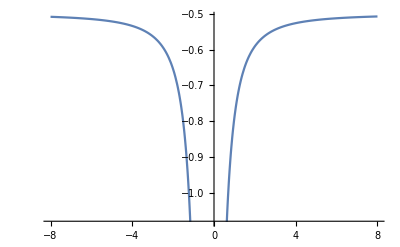

```mathematica
Plot[(√(7/2) (-√14+26 t-11 √14 t^2-14 √14 t^4))/((1-14 t^2)^2),{t,-8,8}]
```

```mathematica
dist/.{x0->1,y0->1,z0->1,x1->2,y1->3,z1->4,xd->1}
```

-(√(7/2) (-(-1+t) (1+t)+√14 √((-1+t)^2 t^2 (1+t)^2)))/(-1+14 t^2)

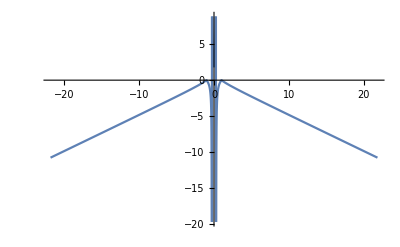

```mathematica
Plot[-(√(7/2) (-(-1+t) (1+t)+√14 √((-1+t)^2 t^2 (1+t)^2)))/(-1+14 t^2),{t,-21.85067147492964,21.8506934302932}]
```

```mathematica
a x0 + b y0 + c z0 == 1
```

a x0+b y0+c z0==1

```mathematica
a x1 + b y1 + c z1 == 1
```

a x1+b y1+c z1==1

```mathematica
a x2 + b y2 + c z2 == 1
```

a x2+b y2+c z2==1

```mathematica
Solve[{Out[31], Out[32], Out[33]}, {a,b,c}]
```

{{a→-(-y1 z0+y2 z0+y0 z1-y2 z1-y0 z2+y1 z2)/(x2 y1 z0-x1 y2 z0-x2 y0 z1+x0 y2 z1+x1 y0 z2-x0 y1 z2),b→-(x1 z0-x2 z0-x0 z1+x2 z1+x0 z2-x1 z2)/(x2 y1 z0-x1 y2 z0-x2 y0 z1+x0 y2 z1+x1 y0 z2-x0 y1 z2),c→-(x1 y0-x2 y0-x0 y1+x2 y1+x0 y2-x1 y2)/(-x2 y1 z0+x1 y2 z0+x2 y0 z1-x0 y2 z1-x1 y0 z2+x0 y1 z2)}}

```mathematica
FullSimplify[-(-y1 z0+y2 z0+y0 z1-y2 z1-y0 z2+y1 z2)/(x2 y1 z0-x1 y2 z0-x2 y0 z1+x0 y2 z1+x1 y0 z2-x0 y1 z2)]
```

(y1 z0-y2 z0-y0 z1+y2 z1+y0 z2-y1 z2)/(x2 y1 z0-x1 y2 z0-x2 y0 z1+x0 y2 z1+x1 y0 z2-x0 y1 z2)

```mathematica
paths=Out[25]
```

((-2 t (x0-x1) xd^3 ((y0-y1)^2+(z0-z1)^2)-(x0-x1)^2 xd^4 √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)+t^2 xd^2 (2 (x0-x1)^2-(y0-y1)^2-(z0-z1)^2) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)-t^4 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)^(3/2)) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))/(2 ((x0-x1)^2 xd^2-t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))^2)

```mathematica
x=x0+k(x1-x0)
```

x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))

```mathematica
y=y0+k(y1-y0)
```

y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))

```mathematica
z=z0+k(z1-z0)
```

z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))

```mathematica
dp1=a(x-xs)+b(y-ys)+c(z-zs)
```

a (x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+b (y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+c (z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))

```mathematica
af1=1/(2 Pi ((x-xs)^2+(y-ys)^2+(z-zs)^2)^(3/2))
```

1/(2 π ((x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2)^(3/2))

```mathematica
l1=af1*dp1
```

(a (x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+b (y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+c (z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))))/(2 π ((x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2)^(3/2))

```mathematica
dp2=a(xt-x)+b(yt-y)+c(zt-z)
```

a (-x0+xt+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+b (-y0+yt+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+c (-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))+zt)

```mathematica
af2=1/(2 Pi ((xt-x)^2+(yt-y)^2+(zt-z)^2)^(3/2))
```

1/(2 π ((-x0+xt+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-y0+yt+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))+zt)^2)^(3/2))

```mathematica
l2=dp2*af2
```

(a (-x0+xt+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+b (-y0+yt+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+c (-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))+zt))/(2 π ((-x0+xt+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-y0+yt+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))+zt)^2)^(3/2))

```mathematica
I = paths*l1*l2
```

((-2 t (x0-x1) xd^3 ((y0-y1)^2+(z0-z1)^2)-(x0-x1)^2 xd^4 √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)+t^2 xd^2 (2 (x0-x1)^2-(y0-y1)^2-(z0-z1)^2) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)-t^4 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)^(3/2)) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2) (a (x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+b (y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+c (z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))) (a (-x0+xt+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+b (-y0+yt+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+c (-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))+zt)))/(8 π^2 ((x0-x1)^2 xd^2-t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))^2 ((x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2)^(3/2) ((-x0+xt+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-y0+yt+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))+zt)^2)^(3/2))

```mathematica
dp2=at(xt-x)+bt(yt-y)+ct(zt-z)
```

at (-x0+xt+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+bt (-y0+yt+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+ct (-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))+zt)

```mathematica
In[44]
```

1/(2 π ((-x0+xt+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-y0+yt+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))+zt)^2)^(3/2))

```mathematica
In[45]
```

(at (-x0+xt+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+bt (-y0+yt+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+ct (-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))+zt))/(2 π ((-x0+xt+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-y0+yt+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))+zt)^2)^(3/2))

```mathematica
In[46]
```

((-2 t (x0-x1) xd^3 ((y0-y1)^2+(z0-z1)^2)-(x0-x1)^2 xd^4 √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)+t^2 xd^2 (2 (x0-x1)^2-(y0-y1)^2-(z0-z1)^2) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)-t^4 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)^(3/2)) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2) (a (x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+b (y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+c (z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))) (at (-x0+xt+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+bt (-y0+yt+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+ct (-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))+zt)))/(8 π^2 ((x0-x1)^2 xd^2-t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))^2 ((x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2)^(3/2) ((-x0+xt+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-y0+yt+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))+zt)^2)^(3/2))

```mathematica
xt=0
```

0

```mathematica
yt=0
```

0

```mathematica
zt=0
```

0

```mathematica
yd=0
```

0

```mathematica
zd=0
```

0

```mathematica
Out[50]
```

((-2 t (x0-x1) xd^3 ((y0-y1)^2+(z0-z1)^2)-(x0-x1)^2 xd^4 √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)+t^2 xd^2 (2 (x0-x1)^2-(y0-y1)^2-(z0-z1)^2) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)-t^4 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)^(3/2)) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2) (a (x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+b (y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+c (z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))) (at (-x0+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+bt (-y0+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+ct (-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))))/(8 π^2 ((x0-x1)^2 xd^2-t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))^2 ((x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2)^(3/2) ((-x0+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-y0+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2)^(3/2))

```mathematica
xt=xd
```

xd

```mathematica
((-2 t (x0-x1) xd^3 ((y0-y1)^2+(z0-z1)^2)-(x0-x1)^2 xd^4 √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)+t^2 xd^2 (2 (x0-x1)^2-(y0-y1)^2-(z0-z1)^2) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)-t^4 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)^(3/2)) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2) (a (x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+b (y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+c (z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))) (at (-x0+xt+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+bt (-y0+yt+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+ct (-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))+zt)))/(8 π^2 ((x0-x1)^2 xd^2-t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))^2 ((x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2)^(3/2) ((-x0+xt+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-y0+yt+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)))+zt)^2)^(3/2))
```

((-2 t (x0-x1) xd^3 ((y0-y1)^2+(z0-z1)^2)-(x0-x1)^2 xd^4 √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)+t^2 xd^2 (2 (x0-x1)^2-(y0-y1)^2-(z0-z1)^2) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)-t^4 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2)^(3/2)) √((x0-x1)^2+(y0-y1)^2+(z0-z1)^2) (a (x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+b (y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+c (z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))) (at (-x0+xd+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+bt (-y0+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))+ct (-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))))/(8 π^2 ((x0-x1)^2 xd^2-t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))^2 ((x0-((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(y0-((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(z0-(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2)^(3/2) ((-x0+xd+((-x0+x1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-y0+((-y0+y1) ((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2+(-z0+(((x0-x1) (t-xd) xd (t+xd)+√(t^2 (t-xd)^2 (t+xd)^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))) (-z0+z1))/(2 (-(x0-x1)^2 xd^2+t^2 ((x0-x1)^2+(y0-y1)^2+(z0-z1)^2))))^2)^(3/2))